```mathematica
vmax=11;
p=0.1;
rho=Round[(1-p)/(vmax+1-2*p),0.001];
dmin=Round[rho*0.1,0.001];
dmax=Round[rho*1.2,0.001];
dd=Round[(dmax-dmin)/22,0.001];
rho " :Transition density!!!"
dmin ": Min density"
dmax ": Max density"
dd ": density step"
"List of simulated values:"
For[i=-1,i<21,i++;
Print[dmin+i*dd]
]
For[i=1,i<4,i++;
Print[i*rho]
]
```

0.076  :Transition density!!!

0.008 : Min density

0.091 : Max density

0.004 : density step

List of simulated values:

0.008

0.012

0.016

0.02

0.024

0.028

0.032

0.036

0.04

0.044

0.048

0.052

0.056

0.06

0.064

0.068

0.072

0.076

0.08

0.084

0.088

0.092

0.152

0.228

0.304

0.1

16384. = L

655 = N

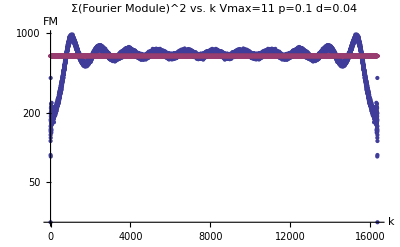

628.853 = N*(L-N)/(L-1)

683.754 = Mean of o.7 largest values

1.03025×10^7 = Sum of All L-1 Valus

1.03025×10^7 = N*(L-N)

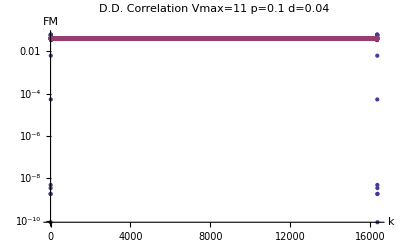

0.0399194 = (N-1)/(L-1)

0.040012 = Mean of o.9 largest values

0.0399194 = Mean of all L-1 values

0.00153946 = STDV of all L-1 values

0.0385641 = STDV/Mean

654. = Sum of All L Valus

654 = N-1

Values lesser than 2/3*(N-1)/(L-1):

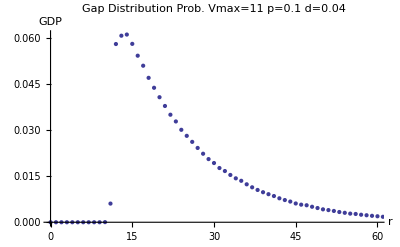

1. =Sum of All values

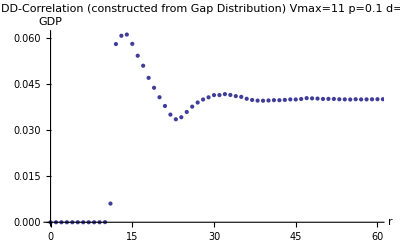

654.567 =Sum of All values

654 = N-1

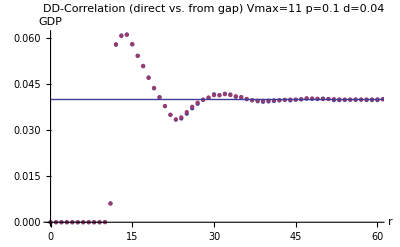

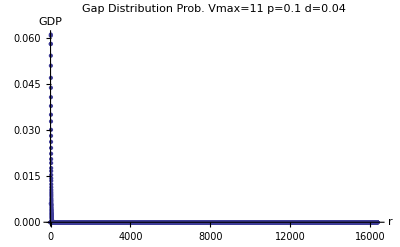

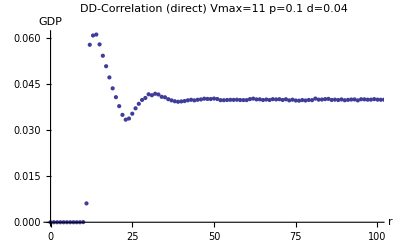

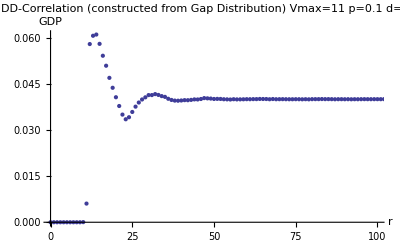

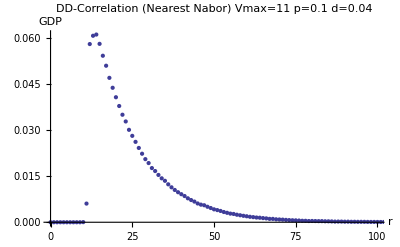

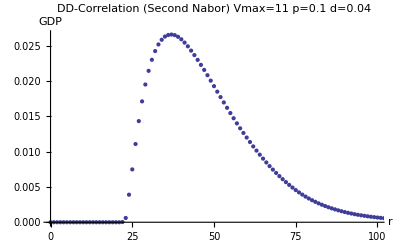

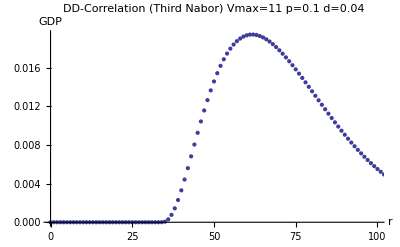

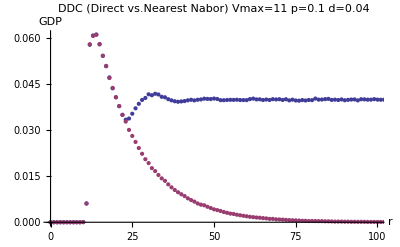

0.000130681 = Mean of first 5*vmax values

0.00327361 = Mean of first 5*vmax values/Random Mean of DDC

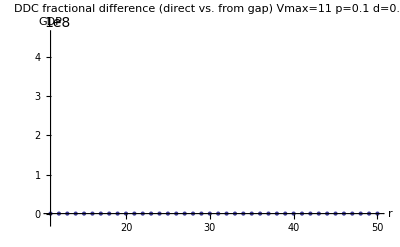

0.00327361

```mathematica
d="0.04";
p="0.1"
vmax="11";
n=16384.000;
a="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short/fourier.1d.averaged.d";
ddc="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short/ddensitycorrelation.d";
ddc1="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short/DDC1.d";ddc2="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short/DDC2.d";
ddc3="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short/DDC3.d";
ddcc="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short/DDCCheck.d";
gap="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short/GapD.d.";
e="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short/ddensitycorrelation.d";
h="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short/DDCCheck.d";
b=".p"<>p<>".v11.txt";
g=".p"<>p<>".v11.txt";
c=a<>d<>b;
l=h<>d<>g;
f=e<>d<>g;
gapadd=gap<>d<>g;
ddcadd=ddc<>d<>g;
ddc1add=ddc1<>d<>g;
ddc2add=ddc2<>d<>g;
ddc3add=ddc3<>d<>g;
ddccadd=ddcc<>d<>g;
DDC=ReadList[ddcadd,{Number,Number}];
DDC1=ReadList[ddc1add,{Number,Number}];
DDC2=ReadList[ddc2add,{Number,Number}];
DDC3=ReadList[ddc3add,{Number,Number}];
DDCC=ReadList[ddccadd,{Number,Number}];
j=StringToStream[d];
o= Read[j,Number];
m=Floor[o*16384];
n "= L"
m  "= N  "
bitF=ReadList[c,{Number,Number}];
DDCCheck=ReadList[l,{Number,Number}];
gapd=ReadList[gapadd,{Number,Number}];
bitf2=bitF[[All,2]];
randomf=Table[{i,(n-m)*m/(n-1)},{i,0,16383}];
ListLogPlot[{bitF,randomf},PlotLabel->"Σ(Fourier Module)^2 vs. k  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{k,FM},PlotRange->Full]
(n-m)*m/(n-1) "= N*(L-N)/(L-1)"
TrimmedMean[bitf2,{0.3,0}] "= Mean of o.7 largest values"
summ=Sum[bitf2[[i]],{i,1,n-1} ];
N[summ] "= Sum of All L-1 Valus"
m*(n-m) "= N*(L-N)"
Δ=summ-m*(n-m);
density=ReadList[f,{Number,Number}];
density2=density[[All,2]];
prand=(m-1)/(n-1);
random=Table[{i,prand},{i,0,16383}];
pic6=ListLogPlot[{density,random},PlotLabel->"D.D. Correlation Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{k,FM},PlotRange->Full]
pic1=ListPlot[density,PlotLabel->"D.D. Correlation Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,DDC},PlotRange->{{0,60},Full}];
pic2=ListLinePlot[random];
prand  "= (N-1)/(L-1)"
TrimmedMean[density2,{0.1,0}] "= Mean of o.9 largest values"
mean=Mean[Delete[density2,1]] "= Mean of all L-1 values"
stdv=StandardDeviation[Delete[density2,1]]  "= STDV of all L-1 values"
StandardDeviation[Delete[density2,1]]/Mean[Delete[density2,1]] "= STDV/Mean"
summ2=Sum[density2[[i]],{i,1,n} ];
N[summ2] "= Sum of All L Valus"
m2=m-1;  
m2 "= N-1"
"Values lesser than 2/3*(N-1)/(L-1):"
ListPlot[gapd,PlotLabel->"Gap Distribution Prob.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP},PlotRange->{{0,60},Full}]
gapd2=gapd[[All,2]];
Sum[gapd2[[i]],{i,1,n}] "=Sum of All values"
pic7=ListPlot[DDCCheck,PlotLabel->"DD-Correlation (constructed from Gap Distribution) Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP},PlotRange->{{0,60},Full}]
pic3=ListPlot[density,PlotLabel->"GDP against DDC  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,"GDP/DDC"},PlotRange->{{0,60},Full}];
DDCCheck2=DDCCheck[[All,2]];
Sum[DDCCheck2[[i]],{i,1,n}] "=Sum of All values"
m2 "= N-1"
pic4=ListLinePlot[gapd];
pic5=ListPlot[gapd,PlotLabel->"Gap Distribution Prob.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP}
,PlotRange->Full];
pic8=ListPlot[{density,DDCCheck},PlotLabel->"DD-Correlation (direct vs. from gap) Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP},PlotRange->{{0,60},Full}];
Show[pic8,pic2]
Show[pic5]
diff=Table[{i,(density2[[i]]-DDCCheck2[[i]])},{i,0,16383}];
diffr=Table[{i,1-DDCCheck2[[i]]/density2[[i]]},{i,0,16383}];
ListPlot[DDC,PlotRange->{{0,100},Full},PlotLabel->"DD-Correlation (direct) Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP}]
ListPlot[DDCC,PlotLabel->"DD-Correlation (constructed from Gap Distribution) Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP},PlotRange->{{0,100},Full}]
ListPlot[DDC1,PlotLabel->"DD-Correlation (Nearest Nabor) Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP},PlotRange->{{0,100},Full}]
ListPlot[DDC2,PlotLabel->"DD-Correlation (Second Nabor) Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP},PlotRange->{{0,100},Full}]
ListPlot[DDC3,PlotLabel->"DD-Correlation (Third Nabor) Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP},PlotRange->{{0,100},Full}]
ListPlot[{DDC,DDC1},PlotLabel->"DDC (Direct vs.Nearest Nabor) Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP},PlotRange->{{0,100},Full}]
SDDC1=DDC1[[All,2]];
SDDC2=DDC2[[All,2]];
SDDC3=DDC3[[All,2]];
Com2=Table[{i-1,SDDC1[[i]]+SDDC2[[i]]},{i,1,100}];
Com3=Table[{i-1,SDDC1[[i]]+SDDC2[[i]]+SDDC3[[i]]},{i,1,100}];
ListPlot[{DDC,Com2},PlotLabel->"DDC (Direct vs.First 2 Nabors) Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP},PlotRange->{{0,100},Full}]
ListPlot[{DDC,Com3},PlotLabel->"DDC (Direct vs.First 3 Nabors) Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP},PlotRange->{{0,100},Full}]
pic11=ListPlot[{DDC,Com3,DDCC},PlotLabel->"DDC (Direct vs. First 2 Nabors vs. approximation) Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP},PlotRange->{{0,100},Full}];
Show[pic11,pic2]
ListPlot[diff,PlotLabel->"DDC difference (direct vs. from gap) Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP},PlotRange->{{0,50},Full}]
diff2=diff[[All,2]];
sum=Sum[Abs[diff2[[i]]],{i,1,55}]/(55);
sum "= Mean of first 5*vmax values"
sum/prand "= Mean of first 5*vmax values/Random Mean of DDC"
ListPlot[diffr,PlotLabel->"DDC fractional difference (direct vs. from gap) Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP},PlotRange->{{11,50},Full}]
sum/prand
```

```mathematica
------------------------------------------------------------------------------------------
```

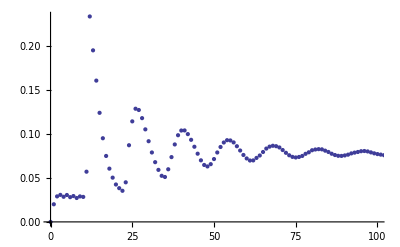

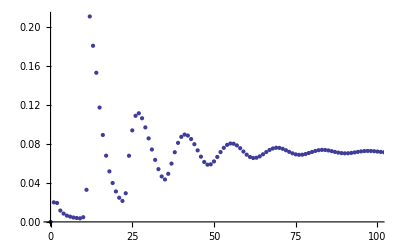

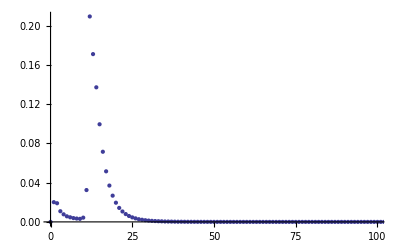

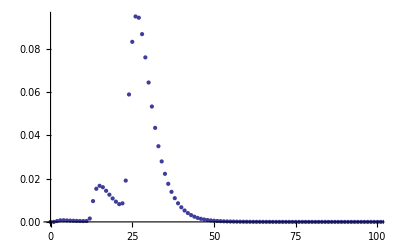

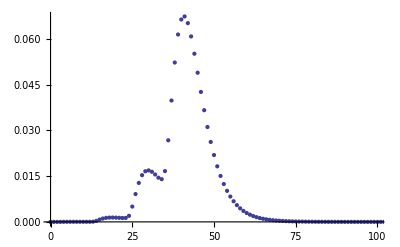

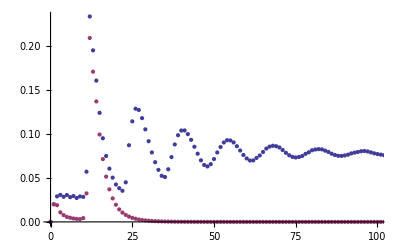

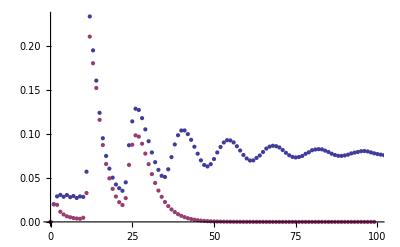

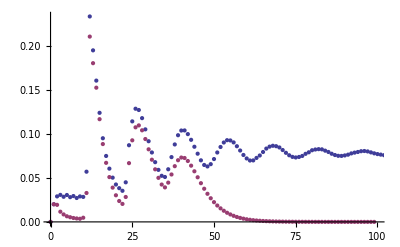

```mathematica
d="0.072";
p="0.1";
vmax="11";
ddc="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short/ddensitycorrelation.d";
ddc1="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short/DDC1.d";ddc2="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short/DDC2.d";
ddc3="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short/DDC3.d";
ddcc="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/short/DDCCheck.d";
b=".p"<>p<>".v11.txt";
ddcadd=ddc<>d<>g;
ddc1add=ddc1<>d<>g;
ddc2add=ddc2<>d<>g;
ddc3add=ddc3<>d<>g;
ddccadd=ddcc<>d<>g;
DDC=ReadList[ddcadd,{Number,Number}];
DDC1=ReadList[ddc1add,{Number,Number}];
DDC2=ReadList[ddc2add,{Number,Number}];
DDC3=ReadList[ddc3add,{Number,Number}];
DDCC=ReadList[ddccadd,{Number,Number}];
ListPlot[DDC,PlotRange->{{0,100},Full}]
ListPlot[DDCC,PlotRange->{{0,100},Full}]
ListPlot[DDC1,PlotRange->{{0,100},Full}]
ListPlot[DDC2,PlotRange->{{0,100},Full}]
ListPlot[DDC3,PlotRange->{{0,100},Full}]
ListPlot[{DDC,DDC1},PlotRange->{{0,100},Full}]
SDDC1=DDC1[[All,2]];
SDDC2=DDC2[[All,2]];
SDDC3=DDC3[[All,2]];
Com2=Table[{i-1,SDDC1[[i]]+SDDC2[[i]]},{i,1,100}];
Com3=Table[{i-1,SDDC1[[i]]+SDDC2[[i]]+SDDC3[[i]]},{i,1,100}];
ListPlot[{DDC,Com2},PlotRange->{{0,100},Full}]
ListPlot[{DDC,Com3},PlotRange->{{0,100},Full}]
ListPlot[{DDC,Com3,DDCC},PlotRange->{{0,100},Full}]
```

```mathematica
Sum[DDCCheck2[[i]],{i,1,n}]
```

1243.98

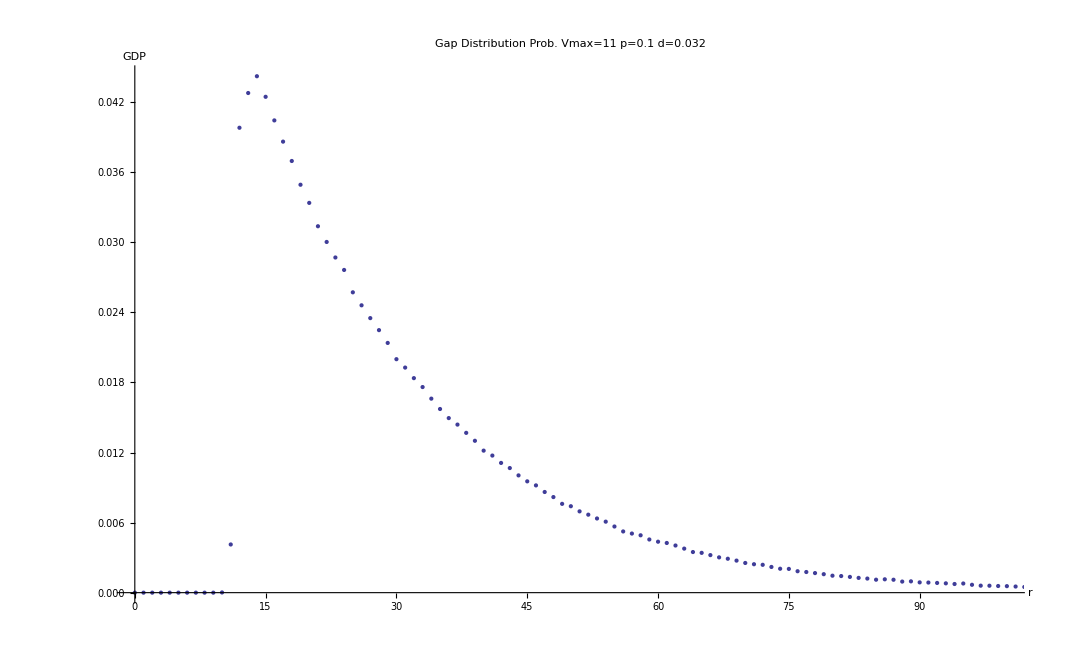

```mathematica
ListPlot[gapd,PlotLabel->"Gap Distribution Prob.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP}
,PlotRange->{{0,100},Full}]
```

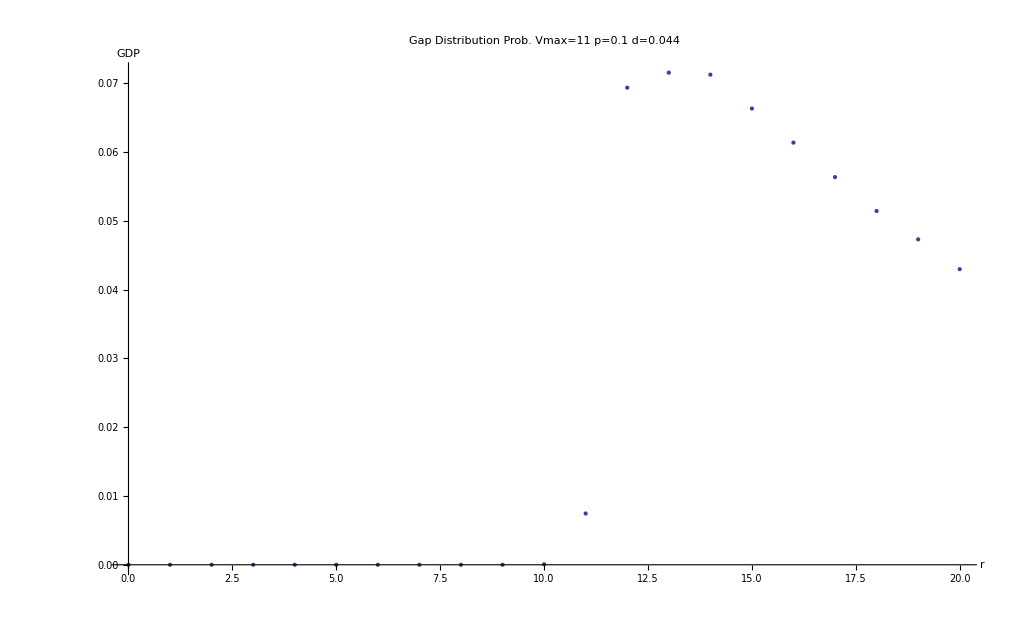

```mathematica
ListPlot[gapd,PlotLabel->"Gap Distribution Prob.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP}
,PlotRange->{{0,20},Full}]
```

```mathematica
gapd
```

{{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0.0000791667},{11,0.00745486},{12,0.0693403},{13,0.0715257},{14,0.0712333},{15,0.0663104},{16,0.0613576},{17,0.0563437},{18,0.0514187},{19,0.0472951},{20,0.0429604},{21,0.0393896},{22,0.0359882},{23,0.0331611},{24,0.0302271},{25,0.0273493},{26,0.0249597},{27,0.022809},{28,0.0209542},{29,0.0191562},{30,0.0173937},{31,0.0160736},{32,0.0146438},{33,0.0133583},«16316»,{16350,0},{16351,0},{16352,0},{16353,0},{16354,0},{16355,0},{16356,0},{16357,0},{16358,0},{16359,0},{16360,0},{16361,0},{16362,0},{16363,0},{16364,0},{16365,0},{16366,0},{16367,0},{16368,0},{16369,0},{16370,0},{16371,0},{16372,0},{16373,0},{16374,0},{16375,0},{16376,0},{16377,0},{16378,0},{16379,0},{16380,0},{16381,0},{16382,0},{16383,0}}

```mathematica
0.1*0.9
```

0.09

```mathematica
0.0715257`+0.09+0.0712333*(1-2*0.09)+0.0663104*0.09
```

0.135905

```mathematica
0.135904942/2
```

0.0679525

```mathematica
g2=gapd[[All,2]];
```

```mathematica
Sum[g2[[i]],{i,1,n-1}]
```

1.

```mathematica
i=14;
pp=0.1*(1-0.1);
g2[[i-1]]*pp+g2[[i]]*(1-2.*pp)+g2[[i+1]]*pp
g2[[i]]
```

0.0713027

0.0715257

```mathematica
i=13
g2[[i]]*0.1+g2[[i+1]]*pp
g2[[i]]
```

13

0.0133713

0.0693403

```mathematica
i=18
(g2[[i-1]]+g2[[i+1]])/2.
g2[[i]]
g2[[i-1]]+g2[[i+1]]-2g2[[i]]
```

18

0.038698

0.0386183

0.0001594

```mathematica
(1-0.09)/0.09*g2[[12]]
```

0.0417179

```mathematica
g2[[13]]
```

0.0398063

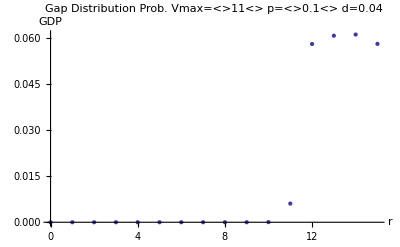

```mathematica
ListPlot[gapd,PlotLabel->"Gap Distribution Prob.  Vmax="<>vmax<>"  p="<>p<>" d="<>  d,AxesLabel->{r,GDP}
,PlotRange->{{0,15},Full}]
```

```mathematica
g2[[12]]*0.09/(1-0.09)
g2[[11]]
```

0.000408061

0.0000171756

```mathematica
g2[[0]]
```

List